## Verify and Plot

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
verifyResults[benchmark_,plot_,plotRange_,verifyTimeLimit_]:= Module[
{systemPath,xvarSet,yvarSet,zvarSet,s1,s2,hPath,hData,h,hHomo,sdpTime,verifyTime,totalTime,result,flag,flagHomo,i},
systemPath=FileNameJoin[{".","Results","problem",StringJoin[benchmark,".txt"]}];
{xvarSet,yvarSet,zvarSet,s1,s2} = ReadList[systemPath];
Print["x Variables: ",xvarSet];
Print["y Variables: ",yvarSet];
Print["z Variables: ",zvarSet];
Print["S1: ",s1];
Print["S2: ",s2];

Print["Verifying results (CAV20 method)..."];
flag =1;
hPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];

(*Length(hData)== 1 if the degree of the template is fixed*)
h = hData[[1]][[1]];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerify[xvarSet, yvarSet, zvarSet, s1,s2,h],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print["Numerical Errors Detected. Invalid Solution."];
flag=0;
];
If[result[[2]]== 1,
Print["Verified."];
Print[h]
];
If[result[[2]]== 2,
Print["Verify out of time."];
Print[h]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

Print["Verifying results (homogenization)..."];
hPath=FileNameJoin[{".","Results","homo",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];
flagHomo=1;
(*Length(hData)== 1 if the degree of the template is fixed*)
h = hData[[1]][[1]];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerifyHomo[xvarSet, yvarSet, zvarSet, s1,s2,h],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print["Numerical Errors Detected. Invalid Solution."];
flagHomo=0
];
If[result[[2]]== 1,
Print["Verified."];
Print[h]
];
If[result[[2]]== 2,
Print["Verify out of time."];
Print[h]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

If[ plot== 1,
If[Length[xvarSet]== 2,myPlot2D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];
If[Length[xvarSet]== 3,myPlot3D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];
]
]

myVerify [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,h_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = And@@(GreaterEqual[#,0]&/@s1);
s2Cons = And@@(GreaterEqual[#,0]&/@s2);
cond1 = FindInstance[h-1< 0&&s1Cons,Join[xvarSet,yvarSet]];
cond2 =FindInstance[-h-1<0&&s2Cons,Join[xvarSet,zvarSet]];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]
myVerifyHomo [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,hHomo_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = And@@(GreaterEqual[#,0]&/@s1);
s2Cons = And@@(GreaterEqual[#,0]&/@s2);
cond1 = FindInstance[hHomo< 0&&s1Cons,Join[xvarSet,yvarSet]];
cond2 =FindInstance[-hHomo< 0&&s2Cons,Join[xvarSet,zvarSet]];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]

myPlot2D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
getRegionSAS[sas_]:=And@@(GreaterEqual[#,0]&/@sas);
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
(*s1Cons=And@@Thread[GreaterEqualThan[0][s1]];
s2Cons=And@@Thread[GreaterEqualThan[0][s2]];*)
s1Plot=RegionPlot[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
hPlot=RegionPlot[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
]


(*inefficient, use other tools*)
myPlot3D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot3D..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
getRegionSAS[sas_]:=And@@(GreaterEqual[#,0]&/@sas);
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
s1Plot=RegionPlot3D[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot3D[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
hPlot=RegionPlot3D[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot3D[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
];
```

## Benchmarks

### 2-d benchmarks

example2d

x Variables: {x,y}

y Variables: {y0}

z Variables: {z0}

S1: {{-2.-2 x^2+2 y^2}}

S2: {{2 x^2-2.2 y^2}}

Verifying results (CAV20 method)...

Verified.

-1.97924-4.04964 x^2+4.25456 y^2

SDP Time: 0.0102722

verify Time: 0.28245

Total Time: 0.292722

Verifying results (homogenization)...

Verified.

-2.38841-5.15737 x^2+5.40724 y^2

SDP Time: 0.0288576

verify Time: 0.320609

Total Time: 0.349467

Plot2d...

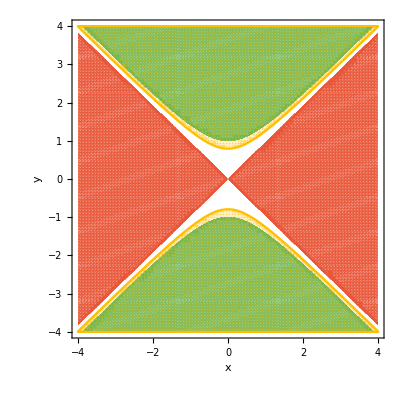

```mathematica
benchmarkname = "example2d";
Print[benchmarkname];
verifytimelimit=1; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-4,4},{-4,4}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

```mathematica
verifyResults
```

verifyResults

### 3-d benchmarks

```mathematica
benchmarkname = "example3d";
Print[benchmarkname];
verifytimelimit=1; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-2,2},{-2,2},{-2,2}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

example3d

x Variables: {x,y,z}

y Variables: {a1,b1,c1,d1}

z Variables: {a2,b2,c2,d2}

S1: {4.-a1^2-b1^2-c1^2-d1^2-x^2-y^2-z^2,-0.01-a1^4+2. x^4-y^4,-1.-b1^2-c1^2-d1^2-x+z^2}

S2: {4.-a2^2-b2^2-c2^2-d2^2-x^2-y^2-z^2,-3.-a2-b2-d2^2+x^2-y,x}

Verifying results (CAV20 method)...

Numerical Errors Detected. Invalid Solution.

SDP Time: 0.452697

verify Time: 0.062629

Total Time: 0.515326

Verifying results (homogenization)...

Verify out of time.

-0.000291904 x-0.50319 x^2-0.0000102561 x y-0.619259 y^2-0.407167 z^2

SDP Time: 0.868077

verify Time: 1.88939

Total Time: 2.75747

Plot3D...

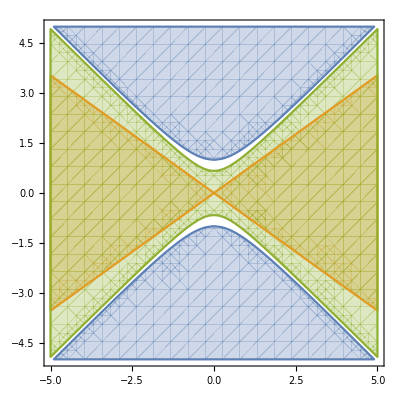

```mathematica
RegionPlot[{y^2-x^2≥ 1, x^2-(1+1)*y^2≥  0,-2.3884061646626096+5.4072386762655835y^2-5.157374112560112x^2≤ 0},{x,-5,5},{y,-5,5}]
```

```mathematica
s1 = {{x,y},{z,w}};
```

(x≥0&&y≥0)||(z≥0&&w≥0)

```mathematica
getRegionSAS[{x,y}]
```

x≥0&&y≥0

$Aborted